```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"RABBIT_Packages"}]];
Needs["MagicMap`"]
myParallelNeeds["MagicMap`"]
SetDirectory[NotebookDirectory[]]
```

D:\Chaozhi\StatisticalPackages\RABBIT Software\RABBIT_Example Scripts

```mathematica
?magicMap
```

magicMap[magicsnp, model, popdesign,ngroup]performs linage map construction in multi-parental populations. The magicsnp specifies the input genotypic data matrix or filename. The model specifies whether the maternally and paternally derived chromosomes are indepdent ("indepModel"), completely dependent ("depModel"), or  modeled jointly ("jointModel"). The popdesign specifies the breeding design information in several possible ways: a list of mating schemes from founder population to the last generation, a list of values denoting the junction distribution, or a filename for population  pedigree information. The ngroup specifies the number of linkage groups.

```mathematica
Options[magicMap]
```

{outputFileID→,isPrintTimeElapsed→True,isRunInParallel→True,founderAllelicError→0.005,offspringAllelicError→0.005,isFounderInbred→True,computingLodType→both,sequenceDataOption→{isFounderAllelicDepth→Automatic,isOffspringAllelicDepth→Automatic,minPhredQualScore→30,priorFounderCallThreshold→0.99},minLodSaving→1,miniComponentSize→5,graphLaplacian→rwNormalized,eigenVectorSelection→eigenratio,nConnectedComponent→1,lodTypeClustering→both,lodTypeOrdering→both,minLodClustering→Automatic,minLodOrdering→Automatic,nNeighborFunction→(√#1&),nNeighborSaving→10,referenceMap→None,delStrongCrossLink→True,minLodSegregateBin→∞,isImputingFounder→True,detectingThreshold→Automatic,imputingThreshold→1,nReplicateAnnealing→1,initTemperature→2,coolingRatio→0.85,freezingTemperature→0.5,deltLoglThreshold→1,maxFreezeIteration→15,dupebinMarker→True,redoSimilarity→True}

```mathematica
dataid="Example"
magicsnpfile=dataid<>"_ObservedGenotype.csv"
model="jointModel";
popdesignfile=dataid<>"_PedigreeInfor.csv"
ngroup=5
```

Example

Example_ObservedGenotype.csv

Example_PedigreeInfor.csv

5

```mathematica
(*take every second marker. set thin =1 using all markers*)
thin=2;
```

```mathematica
magicsnp=Import[magicsnpfile];
(*thinning markers to reduce demonstration time*)
magicsnp=getsubMagicSNP[magicsnp,All,;;;;thin];
refmapfile=Export[dataid<>"_refmap.csv",Transpose[magicsnp[[2;;4]]]]
magicsnp[[3;;4,2;;]]="NA";
magicsnp[[2;;10,;;10]]//MatrixForm
```

Example_refmap.csv

(marker | MN1_29291 | MN1_112907 | MN1_197787 | MN1_444820 | MN1_592863 | BKN118 | CRY2_1021 | AXR1_381 | MN1_1602026
chromosome | NA | NA | NA | NA | NA | NA | NA | NA | NA
pos(cM) | NA | NA | NA | NA | NA | NA | NA | NA | NA
Founder1 | N | 2 | 1 | N | 1 | 1 | 2 | 2 | 2
Founder2 | 2 | 1 | N | 2 | 2 | 2 | 1 | 2 | 1
Founder3 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1
Founder4 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1
ProgenyLine1 | 11 | 11 | 22 | 11 | 22 | 22 | 11 | 11 | NN
ProgenyLine2 | NN | NN | 11 | 11 | 11 | 11 | 22 | 22 | 22)

```mathematica
Options[magicMap]
```

{outputFileID→,isPrintTimeElapsed→True,isRunInParallel→True,founderAllelicError→0.005,offspringAllelicError→0.005,isFounderInbred→True,computingLodType→both,sequenceDataOption→{isFounderAllelicDepth→Automatic,isOffspringAllelicDepth→Automatic,minPhredQualScore→30,priorFounderCallThreshold→0.99},minLodSaving→1,miniComponentSize→5,graphLaplacian→rwNormalized,eigenVectorSelection→eigenratio,nConnectedComponent→1,lodTypeClustering→both,lodTypeOrdering→both,minLodClustering→Automatic,minLodOrdering→Automatic,nNeighborFunction→(√#1&),nNeighborSaving→10,referenceMap→None,delStrongCrossLink→True,minLodSegregateBin→∞,isImputingFounder→True,detectingThreshold→Automatic,imputingThreshold→1,nReplicateAnnealing→1,initTemperature→2,coolingRatio→0.85,freezingTemperature→0.5,deltLoglThreshold→1,maxFreezeIteration→15,dupebinMarker→True,redoSimilarity→True}

-----------------------------------------------------Binning Markers----------------------------------------------------------------

magicsnpBinning. Start date = Thu 25 Apr 2019 09:27:59. Outputfiles = {Example_magicMapOutput_dupebin_magicsnp.csv,Example_magicMapOutput_dupebin_binning.csv,Example_magicMapOutput_dupebin_adjacencymatrix.txt}

#SNPs = 389; #Bins = 389

Done. Finished date = Thu 25 Apr 2019 09:28:02. Time elapsed in magicsnpBinning= 3.43 seconds.

--------------------------------------------------Calculate PairwiseFraction----------------------------------------------------------

magicPairwiseSimilarity. Start date = Thu 25 Apr 2019 09:28:02. Outputfile = Example_magicMapOutput_pairwise_similarity.txt

{#founder, #offspring, #SNP} ={4,150,389}

model is set to "depModel" since the IBD probability = 0.875(>0.85)!

Done! Finished date =Thu 25 Apr 2019 09:28:35. 	Time elapsed in magicPairwiseSimilarity = 32.6 Seconds.

-----------------------------------------------------Construct LinkageMap-------------------------------------------------------------

magicMapConstruct. Start date = Thu 25 Apr 2019 09:28:35. Output map file = Example_magicMapOutput_pairwise_linkagemap.csv

Size of 2 connected componets: {388,1}; dropping components with size <= 5!

The option value of minLodClustering is set to 2.664!

Size of 5 groups = {87,68,70,72,91} and #ungrouped markers = 1 after spectral clustering!Time elapsed = 3.2 Seconds.

The option value of minLodOrdering is set to {2.664, 2.664, 2.664, 2.664, 2.664}!

# NearestNeighbors = {10,9,9,9,10}

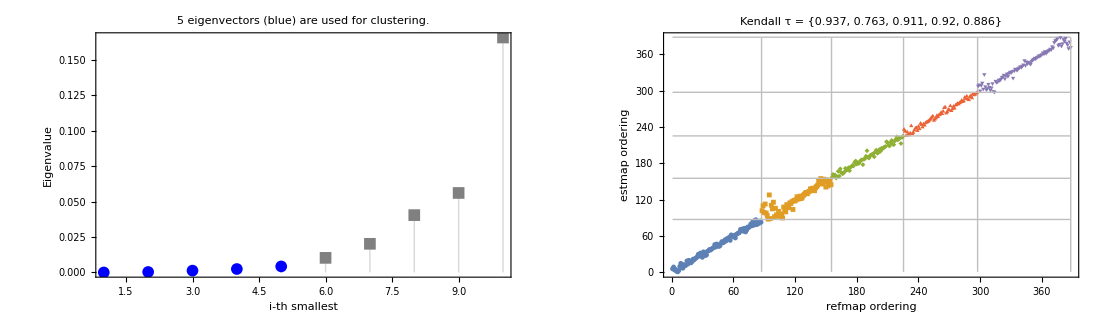

Done! Finished date =Thu 25 Apr 2019 09:28:39. 	Time elapsed in magicMapConstruct = 4.6 Seconds.

-------------------------------------------------------Refine LinkageMap-------------------------------------------------------------

magicMapRefine. Start date = Thu 25 Apr 2019 09:28:39. Outputfiles = {Example_magicMapOutput_refine_linkagemap.csv,Example_magicMapOutput_refine_history.txt}

detectingThreshold is set to 0.9 for jointModel

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={1,2,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={4,1.22825,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={7,0.754299,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={11,0.284484,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={16,0.0248508,True,True,False}

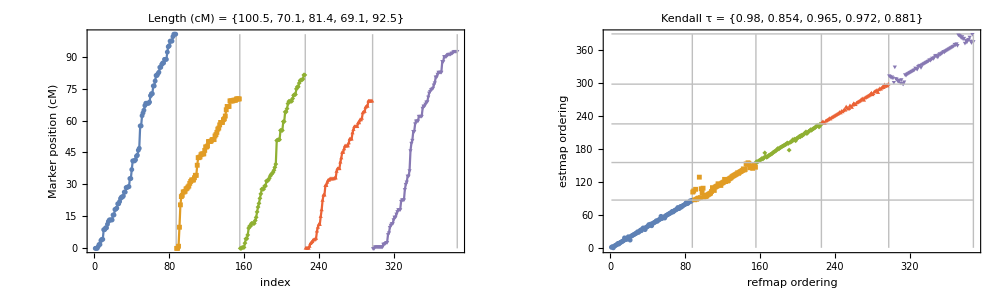

# iterations = {{20},{20},{24},{16},{20}}

Done! Finished date =Thu 25 Apr 2019 09:38:46. 	Time elapsed in magicMapRefine = 606.8 Seconds.

--------------------------------------------------------Export finalMap--------------------------------------------------------------

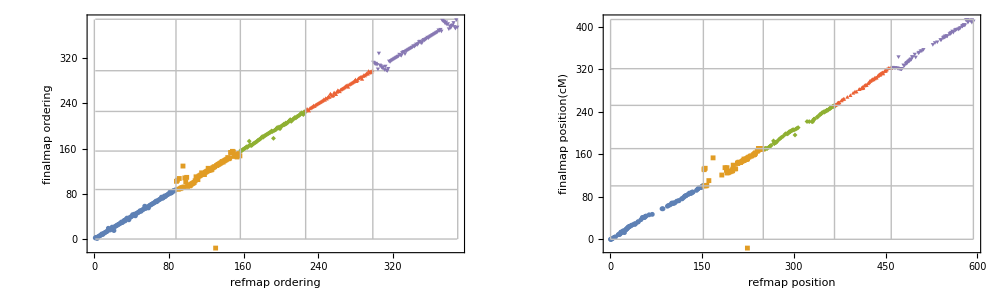

Done. Finished date = Thu 25 Apr 2019 09:38:47.	Time elapsed in all steps of magicMap = 647.97 seconds.

------------------------------------------------------------End---------------------------------------------------------------------

{647.986,Null}

{{Example_magicMapOutput_dupebin_binning.csv,Example_magicMapOutput_dupebin_magicsnp.csv,Example_magicMapOutput_dupebin_adjacencymatrix.txt},Example_magicMapOutput_pairwise_similarity.txt,{Example_magicMapOutput_pairwise_linkagemap.csv},{Example_magicMapOutput_refine_linkagemap.csv,Example_magicMapOutput_refine_history.txt},Example_magicMapOutput_finalmap.csv}

```mathematica
(*refmapfile is used only for monitoring the iterative improvement of genetic map*)
outputfiles=magicMap[magicsnp,model,popdesignfile,ngroup,referenceMap->refmapfile,outputFileID->dataid<>"_magicMapOutput"];//AbsoluteTiming
outputfiles
```

```mathematica
plotHeatMapGUI["Example_magicMapOutput_pairwise_similarity.txt","Example_magicMapOutput_refine_linkagemap.csv"]
```

```mathematica
?plotMapComparison
```

plotMapComparison[estmap, refmap, isordering,linestyle] plot estimated map estmap vs reference map refmap. Comparsons are in terms of marker ordering (isordering = True) or marker position (isordering = False). The style of chromosome boundary lines is specified by linestyle.

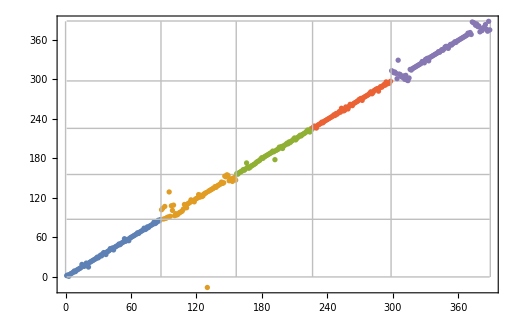

```mathematica
plotMapComparison["Example_refmap.csv","Example_magicMapOutput_finalmap.csv",True,Directive[GrayLevel[0.75],Thin]]
```